# Kepler' s Law Group 1(SCI MATH 101)

#### Evangelia, Luka, Paula, Shaivan

# Notebook 1
Question 1 - Orbits for all planets around the sun,
Q2 - Orbital period (represented via the sin-cos function of the equation as a function of time [t],
Q3 - Calculate the semi-major and semi-minor axes (which are halve of the major and minor axes respectively),
Q4 - Verify Kepler’s Third Law - R^3is proportional to T^2,
Q6 - Orbit for the moon around the earth and orbital period of the moon ,
are answered in this notebook.

```mathematica
(* This defines the coupled differential equations: *)
diffeqns={
x''[t]==-(G M)/(x[t]^2+y[t]^2)x[t]/(√(x[t]^2+y[t]^2)),
y''[t]==-(G M)/(x[t]^2+y[t]^2)y[t]/(√(x[t]^2+y[t]^2))};
```

```mathematica
(* This defines the mass M of the Sun and the value of the gravitational constant: *)
M=1989100×10^24;
G=6.673×10^-11×(1/1000)^3(24×60×60)^2;
(* Perihelion distance (smallest distance to the Sun) in kilometers, maximum orbital velocity in kilometers per second multiplied by a conversion factor to express it in units of kilometers per day: *)
{MercuryDistance,MercuryMaxVelocity}={46.00×10^6,58.98×(24×60×60)};
{VenusDistance,VenusMaxVelocity}={107.48×10^6,35.26×(24×60×60)};
{EarthDistance,EarthMaxVelocity}={147.09×10^6,30.29×(24×60×60)};
{MarsDistance,MarsMaxVelocity}={206.62×10^6,26.50×(24×60×60)};
{JupiterDistance,JupiterMaxVelocity}={740.52×10^6,13.72×(24×60×60)};
{SaturnDistance,SaturnMaxVelocity}={1352.55×10^6,10.18×(24×60×60)};
{UranusDistance,UranusMaxVelocity}={2741.30×10^6,7.11×(24×60×60)};
{NeptuneDistance,NeptuneMaxVelocity}={4444.45×10^6,5.50×(24×60×60)};
{PlutoDistance,PlutoMaxVelocity}={4436.82×10^6,6.10×(24×60×60)};
```

## Question 1 : Generate Orbits for All Planets Question 2 : Find Orbital Period for All Planets (in days) Question 3: Semi-Major and Semi-Minor Axis for All Planets (in km)

```mathematica
(* tmax represents the time period for the simulation with tmax > orbital period for the planet*)
```

## Mercury

### Orbit

```mathematica
(* This defines the initial conditions: *)
initconditionsM={x[0]==MercuryDistance,y[0]==0,x'[0]==0,y'[0]==MercuryMaxVelocity};
(* This defines the set of differential equations and initial conditions: *)
eqnsM=Join[diffeqns,initconditionsM];
(* This solves the differential equations for x and y as a function of t: *)
tmax=100;
solutionM=NDSolve[eqnsM,{x,y},{t,0,tmax},MaxSteps->10000];
(* This plots the orbit of the planet: *)
PorbitM=ParametricPlot[Evaluate[{x[t],y[t]}]/.solutionM,{t,0,tmax},PlotPoints->1000,AspectRatio->Automatic];
(* This plots the orbit of the planet around the centered Sun and shows the planet as a small disk: *)
Manipulate[Show[{PorbitM,Graphics[{Lighter[Red],Disk[Flatten[Evaluate[{x[t],y[t]}]/.solutionM],MercuryDistance/10]}],Graphics[{Yellow,PointSize[0.2], Point[{0,0}]}]}],{t,0,88}]
```

### Orbital period

```mathematica
(* the graph plots the function representing the orbital period of the planet. The distance between 2 consecutive crests respresents 1 approximate orbital period in days
sin-cos function of the equation as a function of time [t] 
one wavelength represents the orbital period ]*)
```

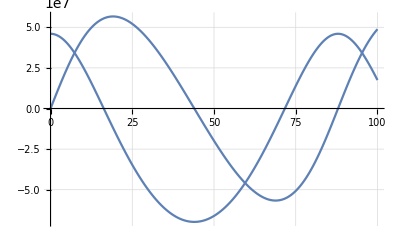

```mathematica
Plot[Evaluate[{x[t],y[t]}]/.solutionM,{t,0,tmax},PlotPoints->1000,GridLines->Automatic]
```

From the graph we can infer that the distance between two consecutive crests is approximately 87 days. 
The actual orbital period is 87.9691 days

### Semi - Major Axis

```mathematica
(* This defines the derivative of the x-position as new function. *)
x2M[t_]=Evaluate[x'[t]/.solutionM][[1]];
```

```mathematica
(* This applies Newton's Method to estimate the zero-crossings of x2[t] *)
(* Or when the derivative equals zero. This corresponds to the extreme values! *)
```

```mathematica
txminM=NestList[(#-x2M[#]/x2M'[#])&,40,5]
```

{40,43.998,43.9738,43.9738,43.9738,43.9738}

```mathematica
txmaxM=NestList[(#-x2M[#]/x2M'[#])&,80,5]
```

{80,91.4598,87.6998,87.9477,87.9476,87.9476}

```mathematica
(* This gets now the minimum and maximum position: *)
```

```mathematica
xminM=Evaluate[x[Last[txminM]]/.solutionM][[1]]
Evaluate[y[Last[txminM]]/.solutionM][[1]];
xmaxM=Evaluate[x[Last[txmaxM]]/.solutionM][[1]]
Evaluate[y[Last[txmaxM]]/.solutionM][[1]];
```

-6.98052×10^7

4.6×10^7

```mathematica
(* This defines the major axis: *)
```

```mathematica
xmaxM-xminM
```

1.15805×10^8

```mathematica
(* semi-major axis is halve of the major axis: major axis/2 *)
```

```mathematica
(* This defines the semi-major axis: *)
```

```mathematica
(1.1580516126449242*^8)/2
```

5.79026×10^7

Length of the semi - major axis of Mercury is 5.790258063224621`*^7 km

### Semi - Minor Axis

```mathematica
(* This defines the derivative of the x-position as new function. *)
y2M[t_]=Evaluate[y'[t]/.solutionM][[1]];
```

```mathematica
(* This applies Newton's Method to estimate the zero-crossings of x2[t] *)
(* Or when the derivative equals zero. This corresponds to the extreme values! *)
```

```mathematica
tyminM=NestList[(#-y2M[#]/y2M'[#])&,60,5]
tymaxM=NestList[(#-y2M[#]/y2M'[#])&,20,5]
```

{60,71.8107,68.9893,68.8385,68.838,68.838}

{20,19.091,19.1096,19.1096,19.1096,19.1096}

```mathematica
(* This gets now the minimum and maximum position: *)
yminM=Evaluate[y[Last[tyminM]]/.solutionM][[1]]
Evaluate[x[Last[tyminM]]/.solutionM][[1]];
ymaxM=Evaluate[y[Last[tymaxM]]/.solutionM][[1]]
Evaluate[x[Last[tymaxM]]/.solutionM][[1]];
```

-5.6666×10^7

5.6666×10^7

```mathematica
(* This defines the minor axis: *)
ymaxM-yminM
```

1.13332×10^8

```mathematica
(* semi-minor axis is the halve of the minor axis: minor axis/2 *)
```

```mathematica
(1.1333203197667608*^8)/2
```

5.6666×10^7

Length of the semi - minor axis of Mercury is 5.666601598833804`*^7 km

## Venus

### Orbit

```mathematica
(* This defines the initial conditions: *)
initconditionsV={x[0]==VenusDistance,y[0]==0,x'[0]==0,y'[0]==VenusMaxVelocity};
(* This defines the set of differential equations and initial conditions: *)
eqnsV=Join[diffeqns,initconditionsV];
```

```mathematica
(* This solves the differential equations for x and y as a function of t: *)
tmax=250;
solutionV=NDSolve[eqnsV,{x,y},{t,0,tmax},MaxSteps->10000];
```

```mathematica
(* This plots the orbit of the planet: *)
PorbitV=ParametricPlot[Evaluate[{x[t],y[t]}]/.solutionV,{t,0,tmax},PlotPoints->1000,AspectRatio->Automatic];
```

```mathematica
(* This plots the orbit of the planet and shows the planet a small disk: *)
Manipulate[Show[{PorbitV,Graphics[{Orange,Disk[Flatten[Evaluate[{x[t],y[t]}]/.solutionV],VenusDistance/10]}],Graphics[{Yellow,PointSize[0.2], Point[{0,0}]}]}],{t,0,224.7}]
```

### Orbital Period

```mathematica
(* the graph plots the function representing the orbital period of the planet. The distance between 2 consecutive crests respresents 1 approximate orbital period in days*)
```

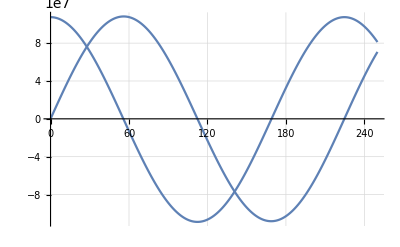

```mathematica
Plot[Evaluate[{x[t],y[t]}]/.solutionV,{t,0,tmax},PlotPoints->1000,GridLines->Automatic]
```

From the graph we can infer that the distance between two consecutive crests is approximately 225 days .
  The actual orbital period is 224.701 days

### Semi - Major Axis

```mathematica
(* This defines the derivative of the x-position as new function. *)
```

```mathematica
x2V[t_]=Evaluate[x'[t]/.solutionV][[1]];
```

```mathematica
txminV=NestList[(#-x2V[#]/x2V'[#])&,100,5]
```

{100,112.835,112.341,112.341,112.341,112.341}

```mathematica
txmaxV=NestList[(#-x2V[#]/x2V'[#])&,200,5]
```

{200,229.742,224.648,224.683,224.683,224.683}

```mathematica
(* This gets now the minimum and maximum position: *)
```

```mathematica
xminV=Evaluate[x[Last[txminV]]/.solutionV][[1]]
Evaluate[y[Last[txminV]]/.solutionV][[1]];
xmaxV=Evaluate[x[Last[txmaxV]]/.solutionV][[1]]
Evaluate[y[Last[txmaxV]]/.solutionV][[1]];
```

-1.08937×10^8

1.0748×10^8

```mathematica
(* This defines the major axis: *)
```

```mathematica
xmaxV-xminV
```

2.16417×10^8

```mathematica
(* This defines the semi-major axis: *)
(2.16417247108741*^8)/2
```

1.08209×10^8

The semi - major axis of Venus' orbit around the sun is 1.082086235543705`*^8 km

### Semi - Minor Axis

```mathematica
(* semi-minor axis calculated in a similar fashion as for Mercury *)
```

```mathematica
y2V[t_]=Evaluate[y'[t]/.solutionV][[1]];
```

```mathematica
tyminV=NestList[(#-y2V[#]/y2V'[#])&,150,5]
```

{150,170.781,168.752,168.753,168.753,168.753}

```mathematica
tymaxV=NestList[(#-y2V[#]/y2V'[#])&,50,5]
```

{50,55.975,55.9299,55.9299,55.9299,55.9299}

```mathematica
yminV=Evaluate[y[Last[tyminV]]/.solutionV][[1]]
Evaluate[x[Last[tyminV]]/.solutionV][[1]];
ymaxV=Evaluate[y[Last[tymaxV]]/.solutionV][[1]]
Evaluate[x[Last[tymaxV]]/.solutionV][[1]];
```

-1.08206×10^8

1.08206×10^8

```mathematica
ymaxV-yminV
```

2.16412×10^8

```mathematica
(* this defines the semi-minor axis *)
```

```mathematica
2.1641235079021442*^8/2
```

1.08206×10^8

The semi-minor axis of Venus' orbit around the Sun is 1.0820617539510721`*^8 km

## Earth

### Orbit

```mathematica
(* This defines the initial conditions: *)
initconditionsE={x[0]==EarthDistance,y[0]==0,x'[0]==0,y'[0]==EarthMaxVelocity};
```

```mathematica
(* This defines the set of differential equations and initial conditions: *)
eqnsE=Join[diffeqns,initconditionsE];
```

```mathematica
(* This solves the differential equations for x and y as a function of t: *)
tmax=400;
solutionE=NDSolve[eqnsE,{x,y},{t,0,tmax},MaxSteps->10000];
```

```mathematica
(* This plots the orbit of the planet: *)
PorbitE=ParametricPlot[Evaluate[{x[t],y[t]}]/.solutionE,{t,0,tmax},PlotPoints->1000,AspectRatio->Automatic];
```

```mathematica
(* This plots the orbit of the planet and shows the planet a small disk: *)
Manipulate[Show[{PorbitE,Graphics[{Blue,Disk[Flatten[Evaluate[{x[t],y[t]}]/.solutionE],EarthDistance/10]}],Graphics[{Yellow,PointSize[0.2], Point[{0,0}]}]}],{t,0,365.25}]
```

### Orbital Period

```mathematica
(* the graph plots the function representing the orbital period of the planet. The distance between 2 consecutive crests respresents 1 approximate orbital period in days*)
```

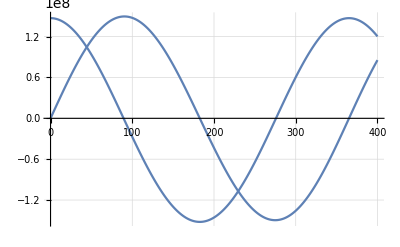

```mathematica
Plot[Evaluate[{x[t],y[t]}]/.solutionE,{t,0,tmax},PlotPoints->1000,GridLines->Automatic]
```

From the graph we can infer that the distance between two consecutive crests is approximately 364 days .
    The actual orbital period is 365.256 days

### Semi - Major Axis

```mathematica
(* same calculation as done previously but changing the variables for that of the Earth *)
```

```mathematica
x2E[t_]=Evaluate[x'[t]/.solutionE][[1]];
```

```mathematica
txminE=NestList[(#-x2E[#]/x2E'[#])&,150,5]
```

{150,186.127,182.6,182.604,182.604,182.604}

```mathematica
txmaxE=NestList[(#-x2E[#]/x2E'[#])&,350,5]
```

{350,365.602,365.208,365.208,365.208,365.208}

```mathematica
xminE=Evaluate[x[Last[txminE]]/.solutionE][[1]]
Evaluate[y[Last[txminE]]/.solutionE][[1]];
xmaxE=Evaluate[x[Last[txmaxE]]/.solutionE][[1]]
Evaluate[y[Last[txmaxE]]/.solutionE][[1]];
```

-1.52094×10^8

1.4709×10^8

```mathematica
(* This defines the major axis: *)
```

```mathematica
xmaxE-xminE
```

2.99184×10^8

```mathematica
(* This defines the semi-major axis: *)
```

```mathematica
2.9918413005572855*^8/2
```

1.49592×10^8

Length of the semi - major axis of Earth is 1.4959206502786428`*^8 km

### Semi - Minor Axis

```mathematica
y2E[t_]=Evaluate[y'[t]/.solutionE][[1]];
```

```mathematica
tyminE=NestList[(#-y2E[#]/y2E'[#])&,250,5]
```

{250,276.779,274.879,274.878,274.878,274.878}

```mathematica
tymaxE=NestList[(#-y2E[#]/y2E'[#])&,50,5]
```

{50,97.6937,90.2668,90.3298,90.3298,90.3298}

```mathematica
yminE=Evaluate[y[Last[tyminE]]/.solutionE][[1]]
Evaluate[x[Last[tyminE]]/.solutionE][[1]];
ymaxE=Evaluate[y[Last[tymaxE]]/.solutionE][[1]]
Evaluate[x[Last[tymaxE]]/.solutionE][[1]];
```

-1.49571×10^8

1.49571×10^8

```mathematica
(* This defines the minor axis: *)
```

```mathematica
ymaxE-yminE
```

2.99142×10^8

```mathematica
(* This defines the semi-minor axis: *)
```

```mathematica
2.9914229791575557*^8/2
```

1.49571×10^8

Length of the semi - minot axis of Earth is 1.49571×10^8km

## Mars

### Orbit

```mathematica
(* This defines the initial conditions: *)
initconditionsMars={x[0]==MarsDistance,y[0]==0,x'[0]==0,y'[0]==MarsMaxVelocity};
```

```mathematica
(* This defines the set of differential equations and initial conditions: *)
eqnsMars=Join[diffeqns,initconditionsMars];
```

```mathematica
(* This solves the differential equations for x and y as a function of t: *)
tmax=800;
solutionMars=NDSolve[eqnsMars,{x,y},{t,0,tmax},MaxSteps->10000];
```

```mathematica
(* This plots the orbit of the planet: *)
PorbitMars=ParametricPlot[Evaluate[{x[t],y[t]}]/.solutionMars,{t,0,tmax},PlotPoints->1000,AspectRatio->Automatic];
```

```mathematica
(* This plots the orbit of the planet and shows the planet a small disk: *)
Manipulate[Show[{PorbitMars,Graphics[{Darker[Red],Disk[Flatten[Evaluate[{x[t],y[t]}]/.solutionMars],MarsDistance/15]}],Graphics[{Yellow,PointSize[0.1], Point[{0,0}]}]}],{t,0,687}]
```

### Orbital Period

```mathematica
(* the graph plots the function representing the orbital period of the planet. The distance between 2 consecutive crests respresents 1 approximate orbital period in days*)
```

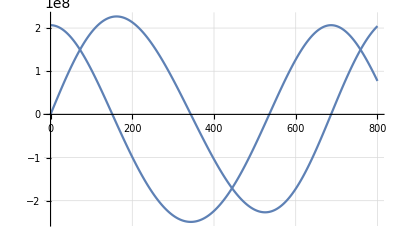

```mathematica
Plot[Evaluate[{x[t],y[t]}]/.solutionMars,{t,0,tmax},PlotPoints->1000,GridLines->Automatic]
```

From the graph we can infer that the distance between two consecutive crests is approximately 690 days
      The actual orbital period is 686.980 days

### Semi - Major Axis

```mathematica
(* same method as done previously and given in the original notebook *)
```

```mathematica
x2Mars[t_]=Evaluate[x'[t]/.solutionMars][[1]];
```

```mathematica
txminMars=NestList[(#-x2Mars[#]/x2Mars'[#])&,300,5]
```

{300,344.575,343.253,343.253,343.253,343.253}

```mathematica
txmaxMars=NestList[(#-x2Mars[#]/x2Mars'[#])&,600,5]
```

{600,731.377,681.795,686.511,686.506,686.506}

```mathematica
xminMars=Evaluate[x[Last[txminMars]]/.solutionMars][[1]]
Evaluate[y[Last[txminMars]]/.solutionMars][[1]];
xmaxMars=Evaluate[x[Last[txmaxMars]]/.solutionMars][[1]]
Evaluate[y[Last[txmaxMars]]/.solutionMars][[1]];
```

-2.49076×10^8

2.0662×10^8

```mathematica
xmaxMars-xminMars
```

4.55696×10^8

```mathematica
(* This defines the semi-major axis: *)
```

```mathematica
4.55695604248873*^8/2
```

2.27848×10^8

Length of the semi-major axis of Mars is 2.27848×10^8km

### Semi - Minor Axis

```mathematica
(* same method as done previously and given in the original notebook *)
```

```mathematica
y2Mars[t_]=Evaluate[y'[t]/.solutionMars][[1]];
```

```mathematica
tyminMars=NestList[(#-y2Mars[#]/y2Mars'[#])&,450,5]
```

{450,546.234,525.365,525.059,525.059,525.059}

```mathematica
tymaxMars=NestList[(#-y2Mars[#]/y2Mars'[#])&,100,5]
```

{100,164.136,161.437,161.447,161.447,161.447}

```mathematica
yminMars=Evaluate[y[Last[tyminMars]]/.solutionMars][[1]]
Evaluate[x[Last[tyminMars]]/.solutionMars][[1]];
ymaxMars=Evaluate[y[Last[tymaxMars]]/.solutionMars][[1]]
Evaluate[x[Last[tymaxMars]]/.solutionMars][[1]];
```

-2.26857×10^8

2.26857×10^8

```mathematica
ymaxMars-yminMars
```

4.53714×10^8

```mathematica
(* This defines the semi-minor axis: *)
4.5371357586312044*^8/2
```

2.26857×10^8

Length of the semi-minor axis of Mars is 2.26857×10^8km

## Jupiter

### Orbit

```mathematica
(* This defines the initial conditions: *)
initconditionsJ={x[0]==JupiterDistance,y[0]==0,x'[0]==0,y'[0]==JupiterMaxVelocity};
(* This defines the set of differential equations and initial conditions: *)
eqnsJ=Join[diffeqns,initconditionsJ];
(* This solves the differential equations for x and y as a function of t: *)
tmax=10000;
solutionJ=NDSolve[eqnsJ,{x,y},{t,0,tmax},MaxSteps->10000000];
(* This plots the orbit of the planet: *)
PorbitJ=ParametricPlot[Evaluate[{x[t],y[t]}]/.solutionJ,{t,0,tmax},PlotPoints->1000,AspectRatio->Automatic];
(* This plots the orbit of the planet and shows the planet a small disk: *)
Manipulate[Show[{PorbitJ,Graphics[{Darker[Brown],Disk[Flatten[Evaluate[{x[t],y[t]}]/.solutionJ],JupiterDistance/10]}],Graphics[{Yellow,PointSize[0.2], Point[{0,0}]}]}],{t,0,4332}]
```

### Orbital Period

```mathematica
(* the graph plots the function representing the orbital period of the planet. The distance between 2 consecutive crests respresents 1 approximate orbital period in days*)
```

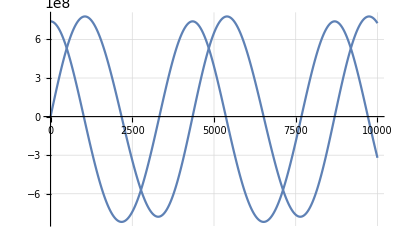

```mathematica
Plot[Evaluate[{x[t],y[t]}]/.solutionJ,{t,0,tmax},PlotPoints->1000,GridLines->Automatic]
```

From the graph we can infer that the distance between two consecutive crests is approximately 4,400 days
      The actual orbital period is 4,332.589 days

### Semi - Major Axis

```mathematica
(* same idea utilised again for the major and minor axes *)
```

```mathematica
x2J[t_]=Evaluate[x'[t]/.solutionJ][[1]];
```

```mathematica
txminJ=NestList[(#-x2J[#]/x2J'[#])&,2000,5]
```

{2000,2175.38,2172.68,2172.68,2172.68,2172.68}

```mathematica
txmaxJ=NestList[(#-x2J[#]/x2J'[#])&,4000,5]
```

{4000,4388.65,4345.28,4345.36,4345.36,4345.36}

```mathematica
xminJ=Evaluate[x[Last[txminJ]]/.solutionJ][[1]]
Evaluate[y[Last[txminJ]]/.solutionJ][[1]];
xmaxJ=Evaluate[x[Last[txmaxJ]]/.solutionJ][[1]]
Evaluate[y[Last[txmaxJ]]/.solutionJ][[1]];
```

-8.18778×10^8

7.4052×10^8

```mathematica
xmaxJ-xminJ
```

1.5593×10^9

```mathematica
(* This defines the semi-major axis: *)
1.5592975484754758*^9/2
```

7.79649×10^8

Length of the semi-major axis of Jupiter’s orbit is 7.79649×10^8km

### Semi - Minor Axis

```mathematica
y2J[t_]=Evaluate[y'[t]/.solutionJ][[1]];
```

```mathematica
tyminJ=NestList[(#-y2J[#]/y2J'[#])&,3000,5]
```

{3000,3321.93,3293.8,3293.73,3293.73,3293.73}

```mathematica
tymaxJ=NestList[(#-y2J[#]/y2J'[#])&,1000,5]
```

{1000,972.456,992.783,1013.2,1068.9,1051.6}

```mathematica
yminJ=Evaluate[y[Last[tyminJ]]/.solutionJ][[1]]
Evaluate[x[Last[tyminJ]]/.solutionJ][[1]];
ymaxJ=Evaluate[y[Last[tymaxJ]]/.solutionJ][[1]]
Evaluate[x[Last[tymaxJ]]/.solutionJ][[1]];
```

-7.78666×10^8

7.78667×10^8

```mathematica
ymaxJ-yminJ
```

1.55733×10^9

```mathematica
(* This defines the semi-minor axis: *)
```

```mathematica
1.5573325232280335*^9/2
```

7.78666×10^8

Length of the semi-minor axis of Jupiter is 7.78666×10^8km

## Saturn

### Orbit

```mathematica
(* This defines the initial conditions: *)
initconditionsS={x[0]==SaturnDistance,y[0]==0,x'[0]==0,y'[0]==SaturnMaxVelocity};
(* This defines the set of differential equations and initial conditions: *)
eqnsS=Join[diffeqns,initconditionsS];
(* This solves the differential equations for x and y as a function of t: *)
tmax=17000;
solutionS=NDSolve[eqnsS,{x,y},{t,0,tmax},MaxSteps->50000];
(* This plots the orbit of the planet: *)
PorbitS=ParametricPlot[Evaluate[{x[t],y[t]}]/.solutionS,{t,0,tmax},PlotPoints->1000,AspectRatio->Automatic];
(* This plots the orbit of the planet and shows the planet a small disk: *)
Manipulate[Show[{PorbitS,Graphics[{Darker[Yellow],Disk[Flatten[Evaluate[{x[t],y[t]}]/.solutionS],SaturnDistance/10]}],Graphics[{Yellow,PointSize[0.2], Point[{0,0}]}]}],{t,0,10780}]
```

### Orbital Period

```mathematica
(* the graph plots the function representing the orbital period of the planet. The distance between 2 consecutive crests respresents 1 approximate orbital period in days*)
```

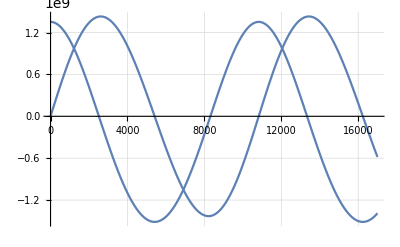

```mathematica
Plot[Evaluate[{x[t],y[t]}]/.solutionS,{t,0,tmax},PlotPoints->1000,GridLines->Automatic]
```

From the graph we can infer that the distance between two consecutive crests is approximately 10,900 days
      The actual orbital period is 10,759.22 days

### Semi - Major Axis

```mathematica
(* similar method used as done previously *)
```

```mathematica
x2S[t_]=Evaluate[x'[t]/.solutionS][[1]];
```

```mathematica
txminS=NestList[(#-x2S[#]/x2S'[#])&,5000,5]
```

{5000,5418.62,5412.92,5412.92,5412.92,5412.92}

```mathematica
txmaxS=NestList[(#-x2S[#]/x2S'[#])&,10000,5]
```

{10000,10923.6,10825.7,10825.8,10825.8,10825.8}

```mathematica
xminS=Evaluate[x[Last[txminS]]/.solutionS][[1]]
Evaluate[y[Last[txminS]]/.solutionS][[1]];
xmaxS=Evaluate[x[Last[txmaxS]]/.solutionS][[1]]
Evaluate[y[Last[txmaxS]]/.solutionS][[1]];
```

-1.51308×10^9

1.35255×10^9

```mathematica
xmaxS-xminS
```

2.86563×10^9

```mathematica
(* This defines the semi-major axis: *)
```

```mathematica
2.865625241717425*^9/2
```

1.43281×10^9

Length of the semi-major axis of Saturn is 1.43281×10^9km

### Semi - Minor Axis

```mathematica
y2S[t_]=Evaluate[y'[t]/.solutionS][[1]];
```

```mathematica
tyminS=NestList[(#-y2S[#]/y2S'[#])&,8000,5]
```

{8000,8219.29,8215.89,8215.89,8215.89,8215.89}

```mathematica
tymaxS=NestList[(#-y2S[#]/y2S'[#])&,2000,5]
```

{2000,2618.72,2609.94,2609.94,2609.94,2609.94}

```mathematica
yminS=Evaluate[y[Last[tyminS]]/.solutionS][[1]]
Evaluate[x[Last[tyminS]]/.solutionS][[1]];
ymaxS=Evaluate[y[Last[tymaxS]]/.solutionS][[1]]
Evaluate[x[Last[tymaxS]]/.solutionS][[1]];
```

-1.43056×10^9

1.43056×10^9

```mathematica
ymaxS-yminS
```

2.86113×10^9

```mathematica
(* This defines the semi-minor axis: *)
```

```mathematica
2.861125658006853*^9/2
```

1.43056×10^9

The length of the semi-minor axis of Saturn is 1.43056×10^9km

## Uranus

### Orbit

```mathematica
(* This defines the initial conditions: *)
initconditionsU={x[0]==UranusDistance,y[0]==0,x'[0]==0,y'[0]==UranusMaxVelocity};
(* This defines the set of differential equations and initial conditions: *)
eqnsU=Join[diffeqns,initconditionsU];
(* This solves the differential equations for x and y as a function of t: *)
tmax=40000;
solutionU=NDSolve[eqnsU,{x,y},{t,0,tmax},MaxSteps->40000];
(* This plots the orbit of the planet: *)
PorbitU=ParametricPlot[Evaluate[{x[t],y[t]}]/.solutionU,{t,0,tmax},PlotPoints->1000,AspectRatio->Automatic];
(* This plots the orbit of the planet and shows the planet a small disk: *)
Manipulate[Show[{PorbitU,Graphics[{Cyan,Disk[Flatten[Evaluate[{x[t],y[t]}]/.solutionU],UranusDistance/15]}],Graphics[{Yellow,PointSize[0.1], Point[{0,0}]}]}],{t,0,30686}]
```

### Orbital Period

```mathematica
(* the graph plots the function representing the orbital period of the planet. The distance between 2 consecutive crests respresents 1 approximate orbital period in days*)
```

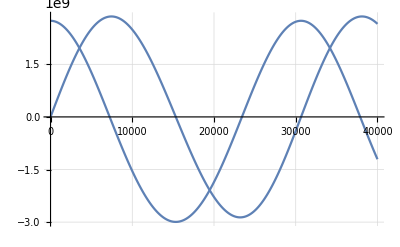

```mathematica
Plot[Evaluate[{x[t],y[t]}]/.solutionU,{t,0,tmax},PlotPoints->1000,GridLines->Automatic]
```

From the graph we can infer that the distance between two consecutive crests is approximately 30,450 days
      The actual orbital period is 30,685.4 days

### Semi - Major Axis

```mathematica
x2U[t_]=Evaluate[x'[t]/.solutionU][[1]];
```

```mathematica
txminU=NestList[(#-x2U[#]/x2U'[#])&,12000,5]
```

{12000,15801.8,15324.7,15325.8,15325.8,15325.8}

```mathematica
txmaxU=NestList[(#-x2U[#]/x2U'[#])&,30000,5]
```

{30000,30656.7,30651.7,30651.7,30651.7,30651.7}

```mathematica
xminU=Evaluate[x[Last[txminU]]/.solutionU][[1]]
Evaluate[y[Last[txminU]]/.solutionU][[1]];
xmaxU=Evaluate[x[Last[txmaxU]]/.solutionU][[1]]
Evaluate[y[Last[txmaxU]]/.solutionU][[1]];
```

-2.99389×10^9

2.7413×10^9

```mathematica
xmaxU-xminU
```

5.73519×10^9

```mathematica
(* This defines the semi-major axis: *)
```

```mathematica
5.735189677764235*^9/2
```

2.86759×10^9

The length of the semi-major axis of Uranus is 2.86759×10^9km

### Semi - Minor Axis

```mathematica
y2U[t_]=Evaluate[y'[t]/.solutionU][[1]];
```

```mathematica
tyminU=NestList[(#-y2U[#]/y2U'[#])&,20000,5]
```

{20000,23890.3,23205.4,23203.6,23203.6,23203.6}

```mathematica
tymaxU=NestList[(#-y2U[#]/y2U'[#])&,6000,5]
```

{6000,7463.85,7448.06,7448.06,7448.06,7448.06}

```mathematica
yminU=Evaluate[y[Last[tyminU]]/.solutionU][[1]]
Evaluate[x[Last[tyminU]]/.solutionU][[1]];
ymaxU=Evaluate[y[Last[tymaxU]]/.solutionU][[1]]
Evaluate[x[Last[tymaxU]]/.solutionU][[1]];
```

-2.86481×10^9

2.86481×10^9

```mathematica
ymaxU-yminU
```

5.72962×10^9

```mathematica
(* This defines the semi-minor axis: *)
```

```mathematica
5.729624917795755*^9/2
```

2.86481×10^9

The length of the semi-minor axis of Uranus is 2.86481×10^9km

## Neptune

### Orbit

```mathematica
(* This defines the initial conditions: *)
initconditionsN={x[0]==NeptuneDistance,y[0]==0,x'[0]==0,y'[0]==NeptuneMaxVelocity};
(* This defines the set of differential equations and initial conditions: *)
eqnsN=Join[diffeqns,initconditionsN];
(* This solves the differential equations for x and y as a function of t: *)
tmax=70000;
solutionN=NDSolve[eqnsN,{x,y},{t,0,tmax},MaxSteps->80000];
(* This plots the orbit of the planet: *)
PorbitN=ParametricPlot[Evaluate[{x[t],y[t]}]/.solutionN,{t,0,tmax},PlotPoints->1000,AspectRatio->Automatic];
(* This plots the orbit of the planet and shows the planet a small disk: *)
Manipulate[Show[{PorbitN,Graphics[{Purple,Disk[Flatten[Evaluate[{x[t],y[t]}]/.solutionN],NeptuneDistance/10]}],Graphics[{Yellow,PointSize[0.2], Point[{0,0}]}]}],{t,0,60189.25}]
```

### Orbital Period

```mathematica
(* the graph plots the function representing the orbital period of the planet. The distance between 2 consecutive crests respresents 1 approximate orbital period in days*)
```

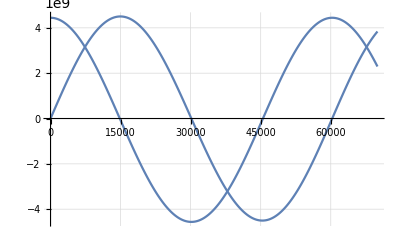

```mathematica
Plot[Evaluate[{x[t],y[t]}]/.solutionN,{t,0,tmax},PlotPoints->1000,GridLines->Automatic]
```

From the graph we can infer that the distance between two consecutive crests is approximately 61,000 days
      The actual orbital period is 60,189 days

### Semi - Major Axis

```mathematica
x2N[t_]=Evaluate[x'[t]/.solutionN][[1]];
```

```mathematica
txminN=NestList[(#-x2N[#]/x2N'[#])&,28000,5]
```

{28000,30187.1,30153.,30153.,30153.,30153.}

```mathematica
txmaxN=NestList[(#-x2N[#]/x2N'[#])&,58000,5]
```

{58000,60355.2,60306.1,60306.1,60306.1,60306.1}

```mathematica
xminN=Evaluate[x[Last[txminN]]/.solutionN][[1]]
Evaluate[y[Last[txminN]]/.solutionN][[1]];
xmaxN=Evaluate[x[Last[txmaxN]]/.solutionN][[1]]
Evaluate[y[Last[txmaxN]]/.solutionN][[1]];
```

-4.5606×10^9

4.44445×10^9

```mathematica
xmaxN-xminN
```

9.00505×10^9

```mathematica
(* This defines the semi-major axis: *)
```

```mathematica
9.005045730864592*^9/2
```

4.50252×10^9

The length of the semi-major axis of Neptune is 4.50252×10^9km

### Semi - Minor Axis

```mathematica
y2N[t_]=Evaluate[y'[t]/.solutionN][[1]];
```

```mathematica
tyminN=NestList[(#-y2N[#]/y2N'[#])&,42000,5]
```

{42000,45519.2,45353.4,45353.4,45353.4,45353.4}

```mathematica
tymaxN=NestList[(#-y2N[#]/y2N'[#])&,14000,5]
```

{14000,14954.,14952.7,14952.7,14952.7,14952.7}

```mathematica
yminN=Evaluate[y[Last[tyminN]]/.solutionN][[1]]
Evaluate[x[Last[tyminN]]/.solutionN][[1]];
ymaxN=Evaluate[y[Last[tymaxN]]/.solutionN][[1]]
Evaluate[x[Last[tymaxN]]/.solutionN][[1]];
```

-4.50215×10^9

4.50215×10^9

```mathematica
ymaxN-yminN
```

9.0043×10^9

```mathematica
(* This defines the semi-minor axis: *)
```

```mathematica
9.004297201320944*^9/2
```

4.50215×10^9

The length of the semi-minor axis of Neptune is 4.50215×10^9km

## Pluto

### Orbit

```mathematica
(* This defines the initial conditions: *)
initconditionsP={x[0]==PlutoDistance,y[0]==0,x'[0]==0,y'[0]==PlutoMaxVelocity};
(* This defines the set of differential equations and initial conditions: *)
eqnsP=Join[diffeqns,initconditionsP];
(* This solves the differential equations for x and y as a function of t: *)
tmax=100000;
solutionP=NDSolve[eqnsP,{x,y},{t,0,tmax},MaxSteps->10000];
(* This plots the orbit of the planet: *)
PorbitP=ParametricPlot[Evaluate[{x[t],y[t]}]/.solutionP,{t,0,tmax},PlotPoints->1000,AspectRatio->Automatic];
(* This plots the orbit of the planet and shows the planet a small disk: *)
Manipulate[Show[{PorbitP,Graphics[{Lighter[Orange],Disk[Flatten[Evaluate[{x[t],y[t]}]/.solutionP],PlutoDistance/15]}],Graphics[{Yellow,PointSize[0.1], Point[{0,0}]}]}],{t,0,90560}]
```

### Orbital Period

```mathematica
(* the graph plots the function representing the orbital period of the planet. The distance between 2 consecutive crests respresents 1 approximate orbital period in days*)
```

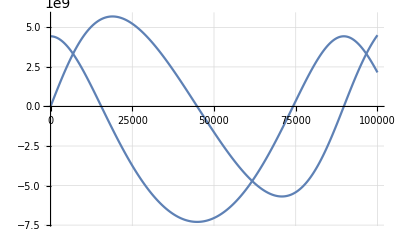

```mathematica
Plot[Evaluate[{x[t],y[t]}]/.solutionP,{t,0,tmax},PlotPoints->1000,GridLines->Automatic]
```

From the graph we can infer that the distance between two consecutive crests is approximately 90, 000 days
      The actual orbital period is 90,560 days

### Semi - Major Axis

```mathematica
x2P[t_]=Evaluate[x'[t]/.solutionP][[1]];
```

```mathematica
txminP=NestList[(#-x2P[#]/x2P'[#])&,40000,5]
```

{40000,44882.3,44854.7,44854.7,44854.7,44854.7}

```mathematica
txmaxP=NestList[(#-x2P[#]/x2P'[#])&,85000,5]
```

{85000,90453.2,89706.6,89709.4,89709.4,89709.4}

```mathematica
xminP=Evaluate[x[Last[txminP]]/.solutionP][[1]]
Evaluate[y[Last[txminP]]/.solutionP][[1]];
xmaxP=Evaluate[x[Last[txmaxP]]/.solutionP][[1]]
Evaluate[y[Last[txmaxP]]/.solutionP][[1]];
```

-7.29784×10^9

4.43682×10^9

```mathematica
xmaxP-xminP
```

1.17347×10^10

```mathematica
(* This defines the semi-major axis: *)
```

```mathematica
1.1734655181710773*^10/2
```

5.86733×10^9

The length of the semi-major axis of Pluto is 5.86733×10^9km

### Semi - Minor Axis

```mathematica
y2P[t_]=Evaluate[y'[t]/.solutionP][[1]];
```

```mathematica
tyminP=NestList[(#-y2P[#]/y2P'[#])&,65000,5]
```

{65000,71910.1,70794.5,70763.1,70763.,70763.}

```mathematica
tymaxP=NestList[(#-y2P[#]/y2P'[#])&,18000,5]
```

{18000,18924.6,18946.3,18946.3,18946.3,18946.3}

```mathematica
yminP=Evaluate[y[Last[tyminP]]/.solutionP][[1]]
Evaluate[x[Last[tyminP]]/.solutionP][[1]];
ymaxP=Evaluate[y[Last[tymaxP]]/.solutionP][[1]]
Evaluate[x[Last[tymaxP]]/.solutionP][[1]];
```

-5.69027×10^9

5.69027×10^9

```mathematica
ymaxP-yminP
```

1.13805×10^10

```mathematica
(* This defines the semi-minor axis: *)
```

```mathematica
1.1380541259609655*^10/2
```

5.69027×10^9

The length of the semi-minor axis of Pluto is 5.69027×10^9km

## Question 4 : Verify Kepler’s Third Law

According to Kepler’s third law, the cube of the length of the semi-major axis in km (R^3) is proportional to the square of the  orbital period of the planet (T^2)
The semi-major axis is in km and the orbital period in days
Using the calculations performed in question 2 and 3, a relation between R^3 and T^2 can be checked

#### Mercury

```mathematica
semimajorM=5.790258063224621*^7;
```

```mathematica
orbitalperiodM=87.9691;
semimajorM^3/orbitalperiodM^2
```

2.50861×10^19

#### Venus

```mathematica
semimajorV=1.082086235543705*^8;
```

```mathematica
orbitalperiodV=224.701;
```

```mathematica
semimajorV^3/orbitalperiodV^2
```

2.50943×10^19

#### Earth

```mathematica
semimajorE=1.4959206502786428*^8;
```

```mathematica
orbitalperiodE=365.256;
```

```mathematica
semimajorE^3/orbitalperiodE^2
```

2.50918×10^19

#### Mars

```mathematica
semimajorMars=2.278478021244365*^8;
```

```mathematica
orbitalperiodMars=686.980;
```

```mathematica
semimajorMars^3/orbitalperiodMars^2
```

2.50638×10^19

#### Jupiter

```mathematica
semimajorJ=7.796487742377379*^8;
```

```mathematica
orbitalperiodJ=4345.36;
```

```mathematica
semimajorJ^3/orbitalperiodJ^2
```

2.50984×10^19

#### Saturn

```mathematica
semimajorS=1.432812620853246*^9;
```

```mathematica
orbitalperiodS=10825.8;
```

```mathematica
semimajorS^3/orbitalperiodS^2
```

2.50985×10^19

#### Uranus

```mathematica
semimajorU=2.8675948420647297*^9;
```

```mathematica
orbitalperiodU=30651.7;
```

```mathematica
semimajorU^3/orbitalperiodU^2
```

2.50983×10^19

#### Neptune

```mathematica
semimajorN=4.5025228653376465*^9;
```

```mathematica
orbitalperiodN=60306.1;
```

```mathematica
semimajorN^3/orbitalperiodN^2
```

2.50984×10^19

#### Pluto

```mathematica
semimajorP=5.867328109393196*^9;
```

```mathematica
orbitalperiodP=89709.4;
```

```mathematica
semimajorP^3/orbitalperiodP^2
```

2.50984×10^19

The results for  R^3/T^2 for each planet results in more-or-less the same answer of 2.50984×10^19 with slight variation for some planets which could be attributed to variation in semi-major and orbital period values. However, since all result in 2.509×10^19, we can confirm Kepler's Third Law and say that the cube of the semi-major axis is proportional to the square of the orbital period for all planets
R^3/T^2= K (constant) -> 2.50984×10^19-> can verify Keplers Third Law as say that R^3 is proportional to T^2.

## Question 6 : Moon Orbiting the Earth

## Moon

### Orbit

```mathematica
(* the differential equation values are changed for the moon-earth orbit 
mass (M1) and gravitational constant (G1) for the earth are considered instead of †he sun since the moon revolves the earth and we wish to plot the orbit of the moon around the earth here
values for the mass and gravitational force were found via the internet since they were not given *)
```

```mathematica
diffeqns1={
xm''[t]==-(G1 M1)/(xm[t]^2+ym[t]^2)xm[t]/(√(xm[t]^2+ym[t]^2)),
ym''[t]==-(G1 M1)/(xm[t]^2+ym[t]^2)ym[t]/(√(xm[t]^2+ym[t]^2))};
```

```mathematica
M1 = 5.9724× 10^24;
```

```mathematica
G1= 6.673 × 10^-11×(1/1000)^3×(24×60×60)^2;
```

```mathematica
(* peripheral distance between the moon and earth (km) and the moon's orbital velocity (km per day)
These values were obtained online through NASA's website *)
{MoonDistance,MoonMaxVelocity}={0.3633× 10^6,1.082×(24×60×60)};
```

```mathematica
(* initial conditions for the equation *)
initconditionsMoon={xm[0]==MoonDistance,ym[0]==0,xm'[0]==0,ym'[0]==MoonMaxVelocity};
```

```mathematica
(* This defines the set of differential equations and initial conditions: *)
eqns1=Join[diffeqns1,initconditionsMoon];
```

```mathematica
(* This solves the differential equations for x and y as a function of t: tmax > orbital period *)
tmaxm=50;
```

```mathematica
solutionMoon=NDSolve[eqns1,{xm,ym},{t,0,tmaxm},MaxSteps->10000];
```

```mathematica
(* This plots the orbit of the moon: *)
```

```mathematica
PorbitMoon=ParametricPlot[Evaluate[{xm[t],ym[t]}]/.solutionMoon,{t,0,tmaxm},PlotPoints->1000,AspectRatio->Automatic];
```

```mathematica
(* This plots the orbit of the moon around a centered earth and shows the moon a small disk: 
with the orbital period as 28 days *)
Manipulate[Show[{PorbitMoon,Graphics[{Lighter[Black],Disk[Flatten[Evaluate[{xm[t],ym[t]}]/.solutionMoon],MoonDistance/10]}],Graphics[{Blue,PointSize[0.2], Point[{0,0}]}]}],{t,0,28}]
```

### Orbital Period

```mathematica
(* plots the orbital period of the moon
sin-cos function of the equation as a function of time [t]] *)
```

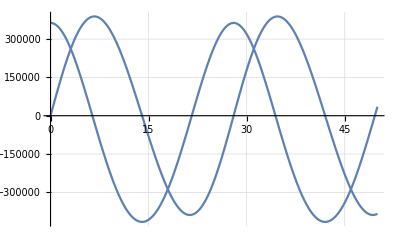

```mathematica
Plot[Evaluate[{xm[t],ym[t]}]/.solutionMoon,{t,0,tmaxm},PlotPoints->1000,GridLines->Automatic]
```

From the sin-cos function above, we can infer that the orbital period (the distance between two consecutive crests) is 28 days.
The actual orbital period is 27.3 days.